```mathematica
(* https://www.janestreet.com/puzzles/current-puzzle/ *)
(*
It’s been a while and change,but the Robot Games are back once again.This time it’s Capture the Flag!
Two robots,Aaron and Erin,have made it to this year’s final! Initially they are situated at the center of a unit circle.A flag is placed somewhere inside the circle,at a location chosen uniformly at random.Once the flag is placed
Aaron is able to deduce its distance to the flag,and Erin is only able to deduce its direction to the flag.(Equivalently:if (r,θ) are the polar coordinates of the flag’s location,Aaron is told r and Erin is told θ.)
Both robots are allowed to make a single move after the flag is placed,if they wish.Any move they make is without knowledge of what the other robot is doing.(And they may not move outside the circle.)

Whichever robot is closer to the flag after these moves captures the flag and is declared the winner!

During the preliminaries it was discovered that Erin is programmed to play a fixed distance along the detected angle θ.Assuming otherwise optimal play by both robots,can you determine the probability that Aaron will win?(Please express your answer to 10 decimal places.)

)*
```

```mathematica
Integrage[1/π, {θ,-π/2,ArcSin[d0/(2r0)]}]
```

Integrage[1/π,{θ,-π/2,ArcSin[d0/(2 r0)]}]

```mathematica
f[x_]=Integrate[2r(x-r),{r,0,x}]+Integrate[2r(r-x),{r,x,1}]
f'[x]
```

2/3-x+(2 x^3)/3

-1+2 x^2

```mathematica
ClearAll["Global`*"];
x0 = 1/(√2);
ans = Integrate[2 r * 1/π*Integrate[1,{θ,0,ArcSin[Abs[x0-r]/(2r)]}]//N,{r,0,1}]
Integrate[2 r * 1/π*Integrate[1,{θ,0,ArcSin[(x0-r)/(2r)]}],{r,0,x0}] + 
Integrate[2 r * 1/π*Integrate[1,{θ,0,ArcSin[(r-x0)/(2r)]}],{r,x0,1}]//FullSimplify
ans//N
```

0.079447-0.0209766 ⅈ

(2 ⅈ √3 π-3 ((-24+6 ⅈ)+6 √(5+2 √2)+4 √3 ArcCosh[2]-36 ArcCsc[2 (2+√2)]+√3 Log[8]-2 √3 Log[6+√2+√(6 (5+2 √2))]))/(108 π)

0.079447-0.0209766 ⅈ

```mathematica
ClearAll["Global`*"];
x0 = 1/(√2)
ans1 = Integrate[2 r * 1/π*ArcSin[Abs[x0-r]/(2r)],{r,1/(3 √2),1}];
ans2 = Integrate[2r,{r,0,1/(3 √2)}];
ans1+ans2
2*(ans1+ans2)//N[#,10]&
```

1/(√2)

1/18+(24-6 √(5+2 √2)-π-4 √3 ArcCosh[2]+36 ArcCsc[2 (2+√2)]-√3 Log[8]+2 √3 Log[6+√2+√(6 (5+2 √2))])/(36 π)

0.214449514

```mathematica
ans1+ans2//N[#,15]&
```

0.107224757023144

1/(√2)

ArcSin[Abs[1/(√2)-r]/(2 r)]/π

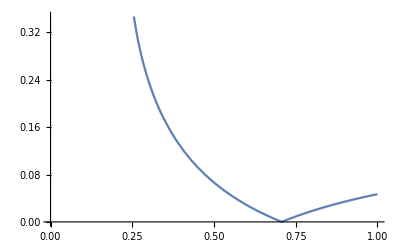

```mathematica
ClearAll["Global`*"];
x0 = 1/(√2)
f[r_]=Integrate[1,{θ,0,ArcSin[Abs[x0-r]/(2r)]}] /π
Plot[f[x],{x,0,1}]
```